## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
Get["SMThreeTraps.m"]
Get["SMThreeChipModel.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

```mathematica
trapzero=(convertCALTableToTrapParameters@tableZLHb)⟦3;;⟧
trapzeroFull=convertCALTableToTrapParameters@tableZLHb
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

```mathematica
trapone=(convertCALTableToTrapParameters@tableZHbB)⟦3;;⟧
traponeFull=convertCALTableToTrapParameters@tableZHbB
```

{0.,2.6,2.6,-1.95,6.14298,-3.11336}

{0.,0.,0.,2.6,2.6,-1.95,6.14298,-3.11336}

### Define target ramp analytic function

```mathematica
(*cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];*)
```

```mathematica
(*omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]*)
```

```mathematica
(*periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*
*)
```

```mathematica
(*num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]*)
```

```mathematica
(*Length@Differences@times*)
```

```mathematica
(*Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]*)
```

```mathematica
(*max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]*)
```

```mathematica
(*dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];*)
```

```mathematica
(*(*InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv=InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv[-max]*)*)
```

```mathematica
(*Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]*)
```

```mathematica
(*corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[1-corgierSimp[t],{t,0,1}]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]*)
```

```mathematica
(*InverseFunction[corgierSimp][8/3]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]*)
```

```mathematica
(*ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N*)
```

```mathematica
(*trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;*)
```

```mathematica
(*Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]*)
```

```mathematica
(*Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]*)
```

```mathematica
(*Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]*)
```

### Define ramp ansatz

#### Trap 1 Short

The first component of this object defines how to distribute the duration of each linear ramp in the ramp sequence. The durations are expressed as a fraction of the ramp sequence’s total duration, and so must sum to 1.

The second component of this object nominally is a guess at the fractional change of the ramp sequence for that linear ramp, but is not used by any of the fitting components and is considered vestigial.

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

Check that both components sum to 1.

```mathematica
Total[rampin1sguess⟦1⟧]
Total[rampin1sguess⟦2⟧]
```

1.

1.

Check the specified number of constituent linear ramps.

```mathematica
Length@rampin1sguess⟦1⟧
```

20

```mathematica
?ChipTrapABFrequencies
```

```mathematica
SingleTrapFrequency[trapzero,trapone,rampin1sguess,Length@rampin1sguess⟦1⟧]
```

{117.929,968.724,929.95}

```mathematica
SingleTrapFrequency[trapzeroFull,traponeFull,rampin1sguess,Length@rampin1sguess⟦1⟧]
```

{118.137,968.904,930.072}

```mathematica
FindTrapEndpoints[trapzeroFull,traponeFull]
```

{473.944,41.0798}

## Calculate ramp

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
(rampin1s=FitCurveHacked[trapzeroFull,traponeFull,rampin1sguess,nramps1short,-3.5,-5])//Timing
```

20

{0.01982,0.27368,0.146498,463.266,463.54,1.,0}

{0.50991,-254.115,0.146498,463.266,209.151,1.,0.01982}

{0.26486,-129.809,0.146498,463.266,333.457,0.50991,0.01982}

{0.14234,-64.6734,0.146498,463.266,398.593,0.26486,0.01982}

{0.08108,-32.0948,0.146498,463.266,431.171,0.14234,0.01982}

{0.05045,-15.8754,0.146498,463.266,447.391,0.08108,0.01982}

{0.03513,-7.78837,0.146498,463.266,455.478,0.05045,0.01982}

{0.02747,-3.75213,0.146498,463.266,459.514,0.03513,0.01982}

{0.02364,-1.73594,0.146498,463.266,461.53,0.02747,0.01982}

{0.02173,-0.730961,0.146498,463.266,462.535,0.02364,0.01982}

{0.02078,-0.231229,0.146498,463.266,463.035,0.02173,0.01982}

Completed point 1 of 19 in 70.9375 s (Total time: 1.18229 min).

{0.0407547,1.30701,0.139291,440.475,441.782,0.9797,0}

{0.51023,-241.024,0.139291,440.475,199.452,0.9797,0.0407547}

{0.27549,-123.318,0.139291,440.475,317.158,0.51023,0.0407547}

{0.15812,-61.106,0.139291,440.475,379.369,0.27549,0.0407547}

{0.09944,-29.8487,0.139291,440.475,410.627,0.15812,0.0407547}

{0.0701,-14.2506,0.139291,440.475,426.225,0.09944,0.0407547}

{0.05543,-6.46673,0.139291,440.475,434.009,0.0701,0.0407547}

{0.04809,-2.57687,0.139291,440.475,437.898,0.05543,0.0407547}

{0.04442,-0.633231,0.139291,440.475,439.842,0.04809,0.0407547}

{0.04259,0.335609,0.139291,440.475,440.811,0.04442,0.0407547}

{0.0435,-0.146136,0.139291,440.475,440.329,0.04442,0.04259}

Completed point 2 of 19 in 70.2656 s (Total time: 2.35339 min).

{0.0634178,1.13999,0.12831,405.751,406.891,0.93666,0}

{0.50004,-221.392,0.12831,405.751,184.359,0.93666,0.0634178}

{0.28173,-114.319,0.12831,405.751,291.433,0.50004,0.0634178}

{0.17257,-56.9615,0.12831,405.751,348.79,0.28173,0.0634178}

{0.11799,-27.932,0.12831,405.751,377.819,0.17257,0.0634178}

{0.0907,-13.3918,0.12831,405.751,392.359,0.11799,0.0634178}

{0.07706,-6.12499,0.12831,405.751,399.626,0.0907,0.0634178}

{0.07024,-2.4926,0.12831,405.751,403.259,0.07706,0.0634178}

{0.06683,-0.676759,0.12831,405.751,405.074,0.07024,0.0634178}

{0.06512,0.233724,0.12831,405.751,405.985,0.06683,0.0634178}

{0.06598,-0.224171,0.12831,405.751,405.527,0.06683,0.06512}

Completed point 3 of 19 in 72.0781 s (Total time: 3.55469 min).

{0.0823724,-0.335151,0.114544,362.22,361.885,0.87111,0}

{0.04119,21.5928,0.114544,362.22,383.813,0.0823724,0}

{0.06178,10.6246,0.114544,362.22,372.845,0.0823724,0.04119}

{0.07208,5.14103,0.114544,362.22,367.361,0.0823724,0.06178}

{0.07723,2.40044,0.114544,362.22,364.62,0.0823724,0.07208}

{0.0798,1.03314,0.114544,362.22,363.253,0.0823724,0.07723}

{0.08109,0.346931,0.114544,362.22,362.567,0.0823724,0.0798}

Completed point 4 of 19 in 47.0938 s (Total time: 4.33958 min).

{0.0924025,-1.47282,0.0995593,314.834,313.361,0.78938,0}

{0.0462,22.8746,0.0995593,314.834,337.709,0.0924025,0}

{0.0693,10.6743,0.0995593,314.834,325.509,0.0924025,0.0462}

{0.08085,4.59388,0.0995593,314.834,319.428,0.0924025,0.0693}

{0.08663,1.55658,0.0995593,314.834,316.391,0.0924025,0.08085}

Completed point 5 of 19 in 34.8281 s (Total time: 4.92005 min).

{0.0950147,-2.78349,0.0849045,268.491,265.708,0.69986,0}

{0.04751,21.6045,0.0849045,268.491,290.096,0.0950147,0}

{0.07126,9.35599,0.0849045,268.491,277.847,0.0950147,0.04751}

{0.08314,3.27,0.0849045,268.491,271.761,0.0950147,0.07126}

{0.08908,0.238053,0.0849045,268.491,268.73,0.0950147,0.08314}

{0.09205,-1.27505,0.0849045,268.491,267.216,0.0950147,0.08908}

{0.09056,-0.516195,0.0849045,268.491,267.975,0.09205,0.08908}

{0.08982,-0.139131,0.0849045,268.491,268.352,0.09056,0.08908}

Completed point 6 of 19 in 53.9219 s (Total time: 5.81875 min).

{0.132962,-4.75116,0.0657551,207.936,203.185,0.61041,0}

{0.06648,27.261,0.0657551,207.936,235.197,0.132962,0}

{0.09972,11.0644,0.0657551,207.936,219.,0.132962,0.06648}

{0.11634,3.10621,0.0657551,207.936,211.042,0.132962,0.09972}

{0.12465,-0.835116,0.0657551,207.936,207.101,0.132962,0.11634}

{0.1205,1.12994,0.0657551,207.936,209.066,0.12465,0.11634}

{0.12258,0.144232,0.0657551,207.936,208.08,0.12465,0.1205}

{0.12362,-0.348011,0.0657551,207.936,207.588,0.12465,0.12258}

{0.1231,-0.10194,0.0657551,207.936,207.834,0.12362,0.12258}

Completed point 7 of 19 in 59.7656 s (Total time: 6.81484 min).

{0.112131,-3.81023,0.0510402,161.403,157.593,0.48757,0}

{0.05607,20.6465,0.0510402,161.403,182.05,0.112131,0}

{0.0841,8.22127,0.0510402,161.403,169.625,0.112131,0.05607}

{0.09812,2.15226,0.0510402,161.403,163.556,0.112131,0.0841}

{0.10513,-0.844005,0.0510402,161.403,160.559,0.112131,0.09812}

{0.10163,0.648754,0.0510402,161.403,162.052,0.10513,0.09812}

{0.10338,-0.0984365,0.0510402,161.403,161.305,0.10513,0.10163}

{0.1025,0.277091,0.0510402,161.403,161.68,0.10338,0.10163}

{0.10294,0.0892762,0.0510402,161.403,161.493,0.10338,0.1025}

Completed point 8 of 19 in 58.7656 s (Total time: 7.79427 min).

{0.0895383,-2.2633,0.0403952,127.741,125.478,0.38441,0}

{0.04477,15.109,0.0403952,127.741,142.85,0.0895383,0}

{0.06715,6.2713,0.0403952,127.741,134.012,0.0895383,0.04477}

{0.07834,1.96665,0.0403952,127.741,129.708,0.0895383,0.06715}

{0.08394,-0.158448,0.0403952,127.741,127.583,0.0895383,0.07834}

{0.08114,0.901657,0.0403952,127.741,128.643,0.08394,0.07834}

{0.08254,0.370992,0.0403952,127.741,128.112,0.08394,0.08114}

{0.08324,0.106119,0.0403952,127.741,127.847,0.08394,0.08254}

Completed point 9 of 19 in 50.3438 s (Total time: 8.63333 min).

{0.0687291,-0.752337,0.032886,103.995,103.242,0.30082,0}

{0.03436,11.1071,0.032886,103.995,115.102,0.0687291,0}

{0.05154,5.08396,0.032886,103.995,109.079,0.0687291,0.03436}

{0.06013,2.14363,0.032886,103.995,106.138,0.0687291,0.05154}

{0.06443,0.689566,0.032886,103.995,104.684,0.0687291,0.06013}

{0.06658,-0.0330181,0.032886,103.995,103.962,0.0687291,0.06443}

{0.0655,0.329584,0.032886,103.995,104.324,0.06658,0.06443}

{0.06604,0.14819,0.032886,103.995,104.143,0.06658,0.0655}

{0.06631,0.0575624,0.032886,103.995,104.052,0.06658,0.06604}

Completed point 10 of 19 in 58.125 s (Total time: 9.60208 min).

{0.053078,-0.234451,0.0276148,87.3256,87.0912,0.23438,0}

{0.02654,8.00358,0.0276148,87.3256,95.3292,0.053078,0}

{0.03981,3.83007,0.0276148,87.3256,91.1557,0.053078,0.02654}

{0.04644,1.78563,0.0276148,87.3256,89.1112,0.053078,0.03981}

{0.04976,0.771946,0.0276148,87.3256,88.0976,0.053078,0.04644}

{0.05142,0.267613,0.0276148,87.3256,87.5932,0.053078,0.04976}

Completed point 11 of 19 in 40.6719 s (Total time: 10.2799 min).

{0.04037,0.0409388,0.0238927,75.5553,75.5962,0.18213,0}

{0.11125,-18.448,0.0238927,75.5553,57.1072,0.18213,0.04037}

{0.07581,-9.52337,0.0238927,75.5553,66.0319,0.11125,0.04037}

{0.05809,-4.82452,0.0238927,75.5553,70.7307,0.07581,0.04037}

{0.04923,-2.41307,0.0238927,75.5553,73.1422,0.05809,0.04037}

{0.0448,-1.19145,0.0238927,75.5553,74.3638,0.04923,0.04037}

{0.04258,-0.575215,0.0238927,75.5553,74.9801,0.0448,0.04037}

{0.04147,-0.266081,0.0238927,75.5553,75.2892,0.04258,0.04037}

{0.04092,-0.112655,0.0238927,75.5553,75.4426,0.04147,0.04037}

{0.04064,-0.0344826,0.0238927,75.5553,75.5208,0.04092,0.04037}

Completed point 12 of 19 in 64.8594 s (Total time: 11.3609 min).

{0.0305638,0.1242,0.0212348,67.1503,67.2745,0.14163,0}

{0.0861,-13.7209,0.0212348,67.1503,53.4294,0.14163,0.0305638}

{0.05833,-6.98521,0.0212348,67.1503,60.1651,0.0861,0.0305638}

{0.04445,-3.4793,0.0212348,67.1503,63.671,0.05833,0.0305638}

{0.03751,-1.69055,0.0212348,67.1503,65.4598,0.04445,0.0305638}

{0.03404,-0.787064,0.0212348,67.1503,66.3633,0.03751,0.0305638}

{0.0323,-0.331713,0.0212348,67.1503,66.8186,0.03404,0.0305638}

{0.03143,-0.103457,0.0212348,67.1503,67.0469,0.0323,0.0305638}

Completed point 13 of 19 in 51.0156 s (Total time: 12.2112 min).

{0.0235214,0.0505359,0.0193111,61.0672,61.1177,0.11063,0}

{0.06708,-10.4306,0.0193111,61.0672,50.6366,0.11063,0.0235214}

{0.0453,-5.3026,0.0193111,61.0672,55.7646,0.06708,0.0235214}

{0.03441,-2.65428,0.0193111,61.0672,58.4129,0.0453,0.0235214}

{0.02897,-1.3101,0.0193111,61.0672,59.7571,0.03441,0.0235214}

{0.02625,-0.632653,0.0193111,61.0672,60.4345,0.02897,0.0235214}

{0.02489,-0.292585,0.0193111,61.0672,60.7746,0.02625,0.0235214}

{0.02421,-0.122213,0.0193111,61.0672,60.945,0.02489,0.0235214}

{0.02387,-0.0369426,0.0193111,61.0672,61.0303,0.02421,0.0235214}

Completed point 14 of 19 in 58.0156 s (Total time: 13.1781 min).

Completed point 15 of 19 in 3. s (Total time: 13.2281 min).

{0.0210217,0.0959645,0.0162959,51.5321,51.6281,0.0688583,0}

{0.04494,-5.32324,0.0162959,51.5321,46.2089,0.0688583,0.0210217}

{0.03298,-2.64812,0.0162959,51.5321,48.884,0.04494,0.0210217}

{0.027,-1.28444,0.0162959,51.5321,50.2477,0.03298,0.0210217}

{0.02401,-0.596171,0.0162959,51.5321,50.9359,0.027,0.0210217}

{0.02252,-0.251599,0.0162959,51.5321,51.2805,0.02401,0.0210217}

{0.02177,-0.0777572,0.0162959,51.5321,51.4544,0.02252,0.0210217}

Completed point 16 of 19 in 46.6719 s (Total time: 14.006 min).

{0.0193771,0.169817,0.0148507,46.9622,47.132,0.0474583,0}

{0.03342,-2.90899,0.0148507,46.9622,44.0532,0.0474583,0.0193771}

{0.0264,-1.38247,0.0148507,46.9622,45.5797,0.03342,0.0193771}

{0.02289,-0.609742,0.0148507,46.9622,46.3524,0.0264,0.0193771}

{0.02113,-0.219945,0.0148507,46.9622,46.7422,0.02289,0.0193771}

{0.02025,-0.0244672,0.0148507,46.9622,46.9377,0.02113,0.0193771}

{0.01981,0.073416,0.0148507,46.9622,47.0356,0.02025,0.0193771}

{0.02003,0.0244624,0.0148507,46.9622,46.9866,0.02025,0.01981}

Completed point 17 of 19 in 51.4844 s (Total time: 14.8641 min).

{0.0152628,0.0916804,0.013767,43.535,43.6267,0.0273183,0}

{0.02129,-1.19177,0.013767,43.535,42.3432,0.0273183,0.0152628}

{0.01828,-0.553284,0.013767,43.535,42.9817,0.02129,0.0152628}

{0.01677,-0.231118,0.013767,43.535,43.3039,0.01828,0.0152628}

{0.01602,-0.0706445,0.013767,43.535,43.4644,0.01677,0.0152628}

Completed point 18 of 19 in 33.6875 s (Total time: 15.4255 min).

{0.00729417,-0.12975,0.0133215,42.1264,41.9966,0.0116783,0}

{0.00365,0.640581,0.0133215,42.1264,42.7669,0.00729417,0}

{0.00547,0.254935,0.0133215,42.1264,42.3813,0.00729417,0.00365}

{0.00638,0.0627999,0.0133215,42.1264,42.1892,0.00729417,0.00547}

{0.00684,-0.0341477,0.0133215,42.1264,42.0922,0.00729417,0.00638}

{0.00661,0.0143111,0.0133215,42.1264,42.1407,0.00684,0.00638}

Completed point 19 of 19 in 39.9688 s (Total time: 16.0917 min).

{967.984,{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.04304,0.06555,0.08173,0.08952,0.08945,0.12284,0.10316,0.08359,0.06644,0.05225,0.0405,0.031,0.0237,0.0180717,0.0214,0.02014,0.01564,0.00672,0.00495833}}}

```mathematica
FindTrapEndpoints[trapzeroFull,traponeFull]
```

{473.944,41.0798}

```mathematica
startptsTest=Table[SingleTrapFrequency[trapzeroFull,traponeFull,{{1},{1}},1,n],{n,2}];
```

```mathematica
(*corgierSin[t_,ωi_,ωf_]:=Module[{tau=2*Pi*t},
ωi+((ωf-ωi)/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[corgierSin[t,1,0],{t,0,1}]*)
```

```mathematica
(*omegaMeanVF[trap0_,trap1_,fColl0_:0,fColl1_:1,deltaFColl_:0.1]:=Module[
{trapParametersVF=Table[trap0+(trap1-trap0)*fColl,{fColl,fColl0,fColl1,deltaFColl}],
omegasVF,omegaMeanVF},
omegasVF=Map[ChipTrapABFrequencies@@#&,trapParametersVF];
Return[Map[GeometricMean[#[[4]]]&,omegasVF]];
];*)
```

```mathematica
Beep[];
```

```mathematica
testRampList={{0,trapzeroFull},{1,traponeFull}};
```

```mathematica
z0AB[#[[2,1]],#[[2,2]],#[[2,3]],#[[2,4]],#[[2,5]],#[[2,6]], #[[2,7]], #[[2,8]]][[All,2]]&/@testRampList
```

{{0.0000743018,-0.0000222095,0.00013569},{0.0000190436,0.000338237,0.000633542}}

```mathematica
(z0AB@@(#[[2,All]]))[[All,2]]&/@testRampList
```

{{0.0000743018,-0.0000222095,0.00013569},{0.0000190436,0.000338237,0.000633542}}

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzeroFull,traponeFull,rampin1s,points1s,nramps1short];)//Timing
```

{277.734,Null}

```mathematica
Length@pts1s
```

101

### Plot calculated ramp’s parameters

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

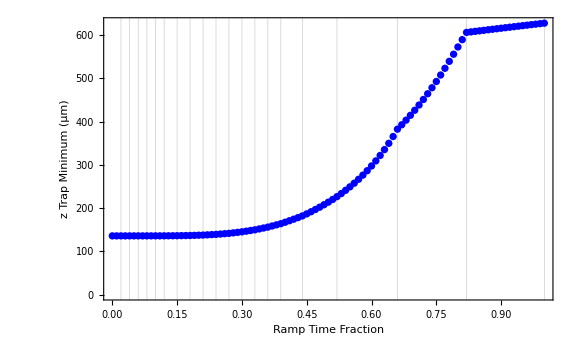
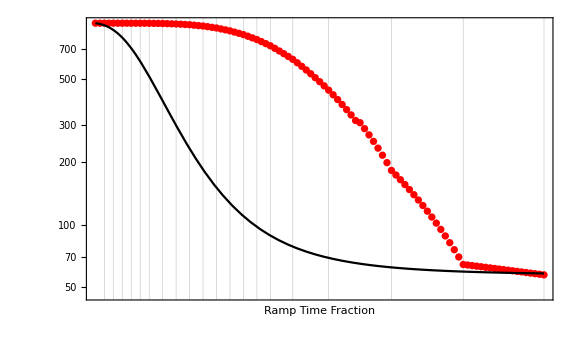

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{2.99006,4.77009}}

{19.8868,117.929}

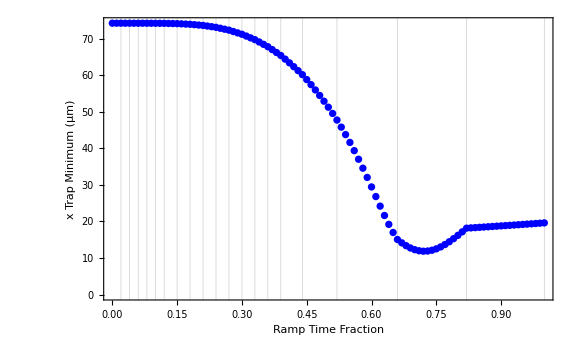
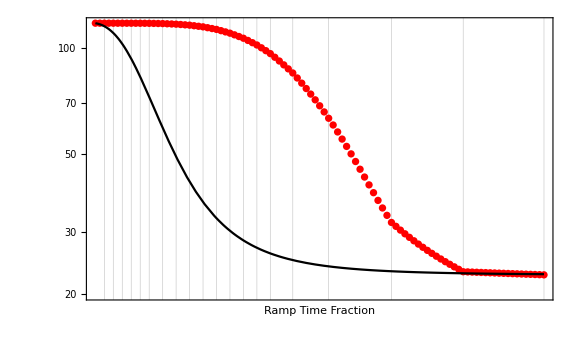

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{3.77149,6.87598}}

{43.4445,968.724}

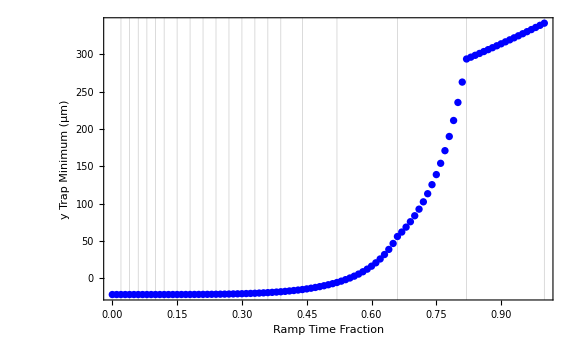
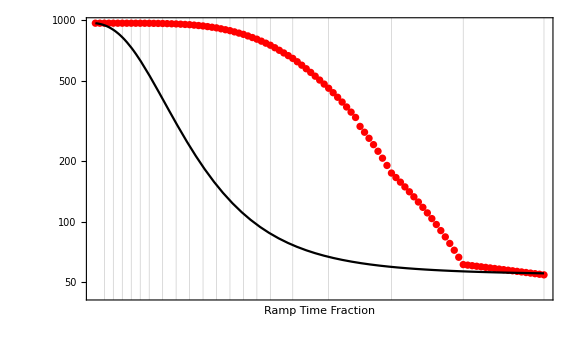

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

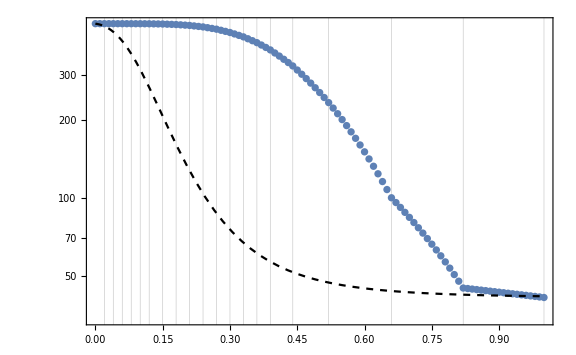

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

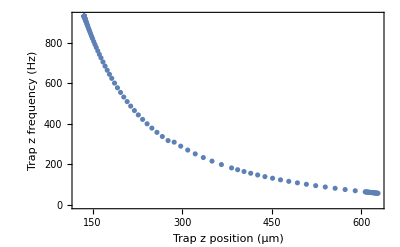

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

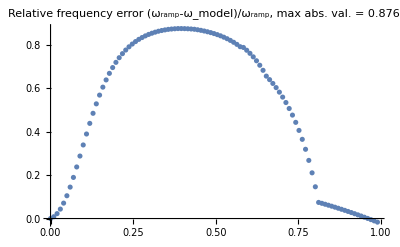

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {19.6048, 341.948, 627.837} μm
Frequency = {22.6293, 54.4236, 57.4638} Hz
Bmin = 4.98191 G

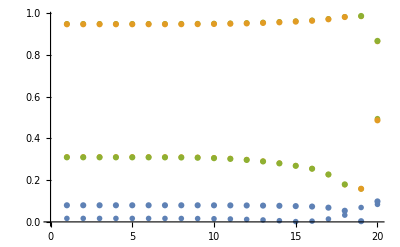

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

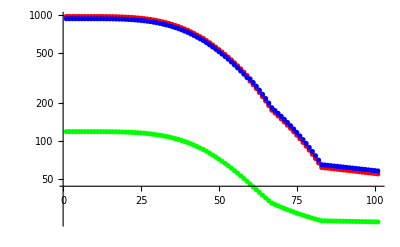

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.00015,0.00023,0.00029,0.00038,0.00058,0.00103,0.00291,0.00705,0.01417,0.02594,0.0433,0.06799,0.09957,0.13925,0.18635,0.28031,0.45713,0.77626,0.98274,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200928T152849

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20200928T152849_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,2.6,2.6,-1.95,6.14298,-3.11336}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20200928T152849_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.,-0.742857,0.52,0.006,0.006,0.142384,0.100095}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.850436}, {0.02, 0.850372}, {0.03, 0.850338}, {0.04, 0.850304}, {0.05, 0.850279}, {0.06, 0.850253}, {0.07, 0.850215}, {0.08, 0.850177}, {0.09, 0.850092}, {0.1, 0.850007}, {0.11, 0.849815}, {0.12, 0.849624}, {0.13, 0.849091}, {0.14, 0.848558}, {0.15, 0.848025}, {0.16, 0.846851}, {0.17, 0.845678}, {0.18, 0.844504}, {0.19, 0.842485}, {0.2, 0.840467}, {0.21, 0.838448}, {0.22, 0.835112}, {0.23, 0.831775}, {0.24, 0.828438}, {0.25, 0.823516}, {0.26, 0.818595}, {0.27, 0.813673}, {0.28, 0.806674}, {0.29, 0.799674}, {0.3, 0.792675}, {0.31, 0.783722}, {0.32, 0.774769}, {0.33, 0.765816}, {0.34, 0.754566}, {0.35, 0.743317}, {0.36, 0.732068}, {0.37, 0.718715}, {0.38, 0.705362}, {0.39, 0.692009}, {0.4, 0.676027}, {0.41, 0.660044}, {0.42, 0.644062}, {0.43, 0.628079}, {0.44, 0.612096}, {0.45, 0.593298}, {0.46, 0.5745}, {0.47, 0.555702}, {0.48, 0.536904}, {0.49, 0.518105}, {0.5, 0.499307}, {0.51, 0.480509}, {0.52, 0.461711}, {0.53, 0.442324}, {0.54, 0.422937}, {0.55, 0.403549}, {0.56, 0.384162}, {0.57, 0.364775}, {0.58, 0.345388}, {0.59, 0.326001}, {0.6, 0.306614}, {0.61, 0.287227}, {0.62, 0.267839}, {0.63, 0.248452}, {0.64, 0.229065}, {0.65, 0.209678}, {0.66, 0.190291}, {0.67, 0.179315}, {0.68, 0.168339}, {0.69, 0.157364}, {0.7, 0.146388}, {0.71, 0.135412}, {0.72, 0.124437}, {0.73, 0.113461}, {0.74, 0.102485}, {0.75, 0.0915095}, {0.76, 0.0805338}, {0.77, 0.0695581}, {0.78, 0.0585824}, {0.79, 0.0476067}, {0.8, 0.036631}, {0.81, 0.0256553}, {0.82, 0.0146796}, {0.83, 0.0138641}, {0.84, 0.0130486}, {0.85, 0.012233}, {0.86, 0.0114175}, {0.87, 0.010602}, {0.88, 0.00978642}, {0.89, 0.00897088}, {0.9, 0.00815535}, {0.91, 0.00733982}, {0.92, 0.00652428}, {0.93, 0.00570874}, {0.94, 0.00489321}, {0.95, 0.00407768}, {0.96, 0.00326214}, {0.97, 0.00244661}, {0.98, 0.00163107}, {0.99, 0.000815535}, {1., 0.}}

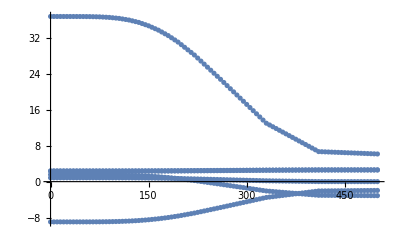

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

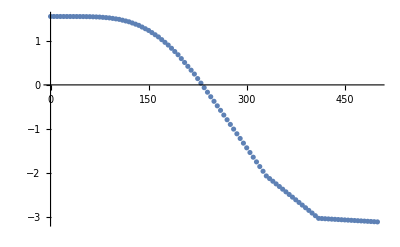

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.00015,0.00008,0.00006,0.00009,0.0002,0.00045,0.00188,0.00414,0.00712,0.01177,0.01736,0.02469,0.03158,0.03968,0.0471,0.09396,0.17682,0.31913,0.20648,0.01726}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.02,0.850372,2.40103,2.30005,-8.93645,36.6676,1.5545},{0.04,0.850304,2.40105,2.30007,-8.93589,36.6651,1.55413},{0.06,0.850253,2.40106,2.30009,-8.93547,36.6633,1.55385},{0.08,0.850177,2.40108,2.30011,-8.93484,36.6606,1.55343},{0.1,0.850007,2.40112,2.30017,-8.93345,36.6545,1.55249},{0.12,0.849624,2.4012,2.30031,-8.9303,36.6407,1.55039},{0.15,0.848025,2.40158,2.30087,-8.91717,36.5833,1.54161},{0.18,0.844504,2.4024,2.30212,-8.88824,36.4569,1.52229},{0.21,0.838448,2.40382,2.30425,-8.83849,36.2396,1.48905},{0.24,0.828438,2.40616,2.30778,-8.75624,35.8802,1.4341},{0.27,0.813673,2.40962,2.31299,-8.63494,35.3502,1.35305},{0.3,0.792675,2.41453,2.3204,-8.46242,34.5965,1.23778},{0.33,0.765816,2.42081,2.32987,-8.24175,33.6324,1.09035},{0.36,0.732068,2.42871,2.34178,-7.96449,32.421,0.905103},{0.39,0.692009,2.43808,2.35591,-7.63538,30.983,0.685214},{0.44,0.612096,2.45678,2.38409,-6.97883,28.1145,0.246556},{0.52,0.461711,2.49197,2.43714,-5.7433,22.7164,-0.578939},{0.66,0.190291,2.55548,2.53288,-3.51338,12.9736,-2.06882},{0.82,0.0146796,2.59657,2.59482,-2.0706,6.66991,-3.03278},{1.,1.11022×10^-16,2.6,2.6,-1.95,6.14298,-3.11336}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.,2.6,2.6,-1.95,6.14298,-3.11336}

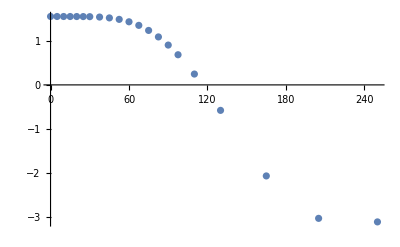

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15